```mathematica
SetDirectory[NotebookDirectory[]];
points = Import["task2\\task2\\in.txt", "Table"][[2;;]];
```

```mathematica
points = Table[{RandomReal[{-20,20}],RandomReal[{-20,20}]},{i,1000}];
```

```mathematica
GetBottomPoint[pts_]:= Module[{points = pts},
points=Sort[points,#1[[2]]<#2[[2]]&];
Return @ points[[1]]
]
GetMaxAnglePoint[pts_, pt_, lastpt_]:= Module[{vectors,angles,cpts},
cpts = Cases[pts, {x_, y_} /; ((x != pt[[1]] || y != pt[[2]]) && (x != lastpt[[1]] || y  != lastpt[[2]]))];
vectors = Partition[Flatten[Table[cpts[[i]] - pt,{i,1,Length@cpts}]],2];
angles = Table[{VectorAngle[vectors[[i]],lastpt - pt], cpts[[i]]},{i,1,Length@vectors}];
angles = Cases[angles,{a_,p_}/;(a!=∞)];

angles = Sort[angles,#1[[1]]>#2[[1]]&];
Return @ angles[[1]][[2]]
]

JarvisAlgorithm[pts_]:=Module[{res},
res = {GetBottomPoint[pts]};
AppendTo[res, GetMaxAnglePoint[pts,res[[1]],res[[-1]] + {-1,0}]];
While[res[[1]]!= res[[-1]],
AppendTo[res, GetMaxAnglePoint[pts,res[[-1]],res[[-2]]]];];
res
]
```

```mathematica
polygon = JarvisAlgorithm[points]
```

{{-12.5317,-19.9821},{9.57946,-19.9157},{15.2212,-19.5867},{17.5086,-18.8053},{19.3463,-16.9499},{19.4582,-16.4038},{19.8339,-13.7325},{19.8767,-10.6269},{19.8555,-2.80721},{19.5702,18.3803},{17.4797,19.5487},{14.1793,19.7412},{1.91602,19.9781},{-15.876,19.9147},{-17.8622,19.7864},{-18.4312,19.3892},{-19.0249,18.333},{-19.6399,17.2184},{-19.9317,14.4668},{-19.9548,10.8661},{-19.9108,-11.4921},{-19.8465,-15.7615},{-19.5837,-19.7383},{-12.5317,-19.9821}}

```mathematica
ClearSystemCache[];
Timing[JarvisAlgorithm[points];]
```

{0.25,Null}

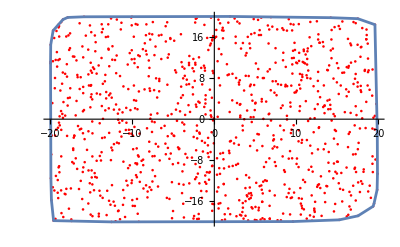

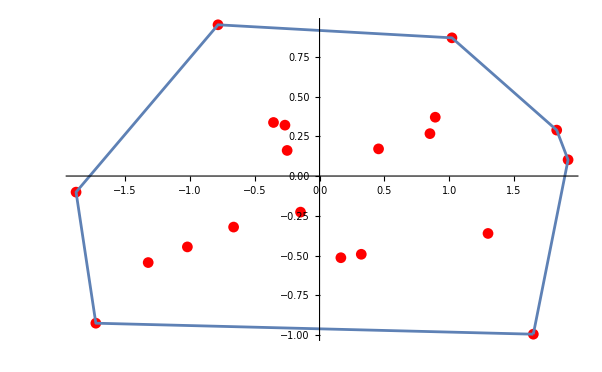

```mathematica
Show[ListPlot[points,PlotStyle->Red], ListLinePlot[polygon], PlotRange->All]
```